# MEASURES AND TESTS OF ASSOCIATION

## DR JHK

## INTRODUCTION

An association is a measurement between two categorical variables

The association between a high-caloric or normal-caloric intake diet and the presence or absence of obesity

Measures of association (note that risk is another synonym for proportion and probability) between an explanatory (exposure or independent) variable and a response (outcome or disease or dependent) variable

Risk difference

Relative risk (risk ratio)

Odds ratio

Hypothesis testing

Pearson’s -test (-test for association or -test for independence)

## REVISITING PROBABILITIES

Consider an exposure variable with categories  and  and a response variable with categories  and  with contingency table below

Two Nominal Variables |  |  | Total
 |  |  | 
 |  |  | 
Total |  |  |

Two conditional probabilities of interest

P̂(D|E)=n_11/(n_(1+))

P̂(D|Ē)=n_21/(n_(2+))

## MEASURES OF ASSOCIATION

Motivating example

Two Nominal Variables |  |  | Total
 |  |  | 
 |  |  | 
Total |  |  |

### RISK DIFFERENCE

Difference in conditional probabilities

OverHat[RD]=P̂(D|E)-P̂(D|Ē)=101/124-21/119≈.638

```mathematica
(*Confirm the calculation*)
pde=101/124;
pdne=21/119;
rdEstimate=N[pde-pdne]
```

0.638046

The estimated risk of disease in the exposed is  percentage points higher than the estimated risk of disease in the unexposed / Exposure increases the risk of disease by  percentage point compared to non-exposure

We can calculate confidence intervals, given that  and where where  is the confidence coefficient for a confidence level of

OverHat[RD]±c √((n_11/(n_(1+))(1-n_11/(n_(1+))))/(n_(1+))+(n_21/(n_(2+))(1-n_21/(n_(2+))))/(n_(2+)))

Under a null hypothesis, the population risk difference would be  percentage points and the claim (alternative hypothesis) would be that it is not  percentage point

```mathematica
(*Calculate the confidence coefficient*)
c=InverseCDF[NormalDistribution[],.975];
(*Calculate the standard error*)
seRDEstimate=N[√((pde(1-pde))/124+(pdne (1-pdne))/119)];
(*Calculate the confidence interval*)
rdEstimate-(c seRDEstimate)(*Lower bound*)
rdEstimate+(c seRDEstimate)(*Upper bound*)
```

0.541238

0.734853

We are % confidence that the true population risk difference is between % and %

Since the population risk difference under the null hypothesis is NOT in this interval, we reject the null hypothesis and support the alternative hypothesis

### RISK RATIO (RELATIVE RISK)

Ratio of conditional probabilities

OverHat[RR]=(P̂(D|E))/(P̂(D|Ē))
OverHat[RR]=(101/124)/(21/119)≈4.626

```mathematica
(*Confirm the calculation*)
pde=101/124;
pdne=21/119;
rrEstimate=N[pde/pdne]
```

4.61559

The estimated risk is of disease in the exposed is  times the estimated risk of disease in the unexposed

A simple derivation can express this as a percentage

(P̂(D|E))/(P̂(D|Ē))=4.62
P̂(D|E)=4.62 P̂(D|Ē)
P̂(D|E)=(1+3.62)P̂(D|Ē)
P̂(D|E)=P̂(D|Ē)+3.62 P̂(D|Ē)

The risk of disease in the exposed is  times the risk of disease in the unexposed / Exposure increases the risk of disease by %

We can calculate confidence intervals where where  is the confidence coefficient for a confidence level of

Unfortunately the estimated relative risk is not normally distributed and we have to perform a log transformation

ln(OverHat[RR])±c √(n_12/(n_11(n_11+n_12))+n_22/(n_21(n_21+n_22))

Under a null hypothesis, the population relative risk would be  and the claim (alternative hypothesis) would be that it is not

```mathematica
(*Calculate the confidence coefficient*)
c=InverseCDF[NormalDistribution[],.975];
(*Calculate the standard error*)
seRREstimate=N[√(23/(101 124)+98/(21 119))];
(*Calculate the log confidence interval*)
lbLogRR=Log[rrEstimate]-(c seRREstimate)(*Lower bound*)
ubLogRR=Log[rrEstimate]+(c seRREstimate)(*Upper bound*)
```

1.13233

1.92655

We have to exponentiate these bounds (inverse of the logarithm)

```mathematica
(*Calculate the exponential of the lower bound*)
ⅇ^lbLogRR
(*Calculate the exponential of the upper bound*)
ⅇ^ubLogRR
```

3.10286

6.86582

We are % confidence that the true population relative risk is between  and

Since the population relative risk under the null hypothesis is NOT in this interval, we reject the null hypothesis and support the alternative hypothesis

We can also express these bounds as percentages with a % confidence interval of between 210% and 587% increase in risk

If the estimated relative risk is lower than , we would use the following derivation (where )

(P̂(D|E))/(P̂(D|Ē))=.41
P̂(D|E)=.41 P̂(D|Ē)
P̂(D|E)=(1-.59)P̂(D|Ē)
P̂(D|E)=P̂(D|Ē)-.59 P̂(D|Ē)

We would state that the exposure decreases the risk of disease by %

### ODDS RATIO

Ratio of odds

Odds is the ratio between the probability of success  and the probability of failure  (for a binary variable)

Odds of disease in the exposed

(P̂(D|E))/(1-P̂(D|E))=(P̂(D|E))/(P̂(D̄|E))=(n_11/(n_(1+)))/(n_12/(n_(1+)))

Odds of disease in the unexposed

(P̂(D|Ē))/(1-P̂(D|Ē))=(P̂(D|Ē))/(P̂(D̄|Ē))=(n_21/(n_(2+)))/(n_22/(n_(2+)))

Odds ratio (comparing odds of disease in exposed to odds of disease in unexposed)

((P̂(D|E))/(P̂(D̄|E)))/((P̂(D|Ē))/(P̂(D̄|Ē)))=((n_11/(n_(1+)))/(n_12/(n_(1+))))/((n_21/(n_(2+)))/(n_22/(n_(2+))))=(n_11/(n_(1+)))/(n_12/(n_(1+))) (n_22/(n_(2+)))/(n_21/(n_(2+)))=(n_11 n_22)/(n_12 n_21)

We calculate the estimated odds ratio

```mathematica
(*Calculate the estimated odds ratio form the data*)
orEstimate=N[(101 98)/(23 21)]
```

20.4928

We conclude that the odds of disease in the exposed is 20.49 times the odds of disease in the unexposed

The same argument holds as for the relative risk and we state that exposure increases the estimated odds of disease by %

We can calculate confidence intervals where where  is the confidence coefficient for a confidence level of

Unfortunately the estimated odds ratio is not normally distributed and we have to perform a log transformation

ln(OverHat[OR])±c √(1/n_11+1/n_12+1/n_21+1/n_22)

Under a null hypothesis the population odds ratio would be  and the claim (alternative hypothesis) would be that it is not

```mathematica
(*Calculate the confidence coefficient*)
c=InverseCDF[NormalDistribution[],.975];
(*Calculate the standard error*)
seOREstimate=N[√(1/101+1/23+1/21+1/98)];
(*Calculate the log confidence interval*)
lbLogOR=Log[orEstimate]-(c seOREstimate)(*Lower bound*)
ubLogOR=Log[orEstimate]+(c seOREstimate)(*Upper bound*)
```

2.36648

3.67366

We have to exponentiate (anti-logarithm) these bounds (=EXP(2.36648))

```mathematica
(*Calculate the exponential of the lower bound*)
ⅇ^lbLogOR
(*Calculate the exponential of the upper bound*)
ⅇ^ubLogOR
```

10.6598

39.3959

We are % confident that the true population odds ratio is between  and

Since the population odds under the null hypothesis is NOT in this interval, we reject the null hypothesis and support the alternative hypothesis

We can also express these bounds as percentages with a % confidence interval of between 966% and 3840% increase in risk

### OBSERVATIONAL STUDY DESIGN

For risk difference and relative risk we calculate a conditional probability for disease given exposure

and

Disease must be random

In cross-sectional and cohort studies  is random

Relative risk and risk difference is only for cross-sectional and cohort studies

In case-control studies,  is not random (hence  or  is not random)

Only odds ratio can be used

The table below summarizes

| RD | RR | OR
Case-Control | No | No | Yes
Cross-Sectional | Yes | Yes | Yes
Cohort | Yes | Yes | Yes

## HYPOTHESIS TEST FOR ASSOCIATION

Test the association between two categorical variables

Pearson’s -test (-test for association /  test for independence)

### EXAMPLE

Researchers randomize 362 participants to receive either one of two active interventions or a placebo in a population of adults with hypertension

They measure whether the participants improve or not (with respect to their hypertension)

There results are summarized

Two Categorical Variables | Improve | Do Not Improve | Total
Intervention A |  |  | 
Intervention B |  |  | 
Placebo |  |  | 
Total |  |  |

Researchers claim that their is an association between the intervention and the response

Test their clam at the 1% level of significance

SOLUTION

Step 1

The joint proportions in the population

Step 2

: Intervention is not associated with outcome

: Intervention is associated with outcome

Step 3

Step 4

-test for association

Two categorical variables

Independent observations

At least 80% of expected frequencies are  or more

under , where  with k being the number of categories in the exposure variable and l being the number of categories in the response variable

Here

Step 5

Calculating the expected values

Given that events  and  are independent we have that

This is so under the null hypothesis

P(A∩B)=P(A) P(B)
n P(A∩B)=n P(A) P(B)
n P(Active intervention AND improved)=n P(Active intervention) P(Improved)
E_11=n (n_(1+))/n (n_(+1))/n
E_11=(n_(1+)n_(+1))/n
E_ij=(n_(i+)n_(+j))/n

Calculate the expected frequencies under the null hypothesis

Two Categorical Variables | Improve | Do Not Improve | Total
Intervention A |  |  | 
Intervention B |  |  | 
Placebo |  |  | 
Total |  |  |

```mathematica
(*Verify the results*)
N[(124 143)/362]
N[(124 219)/362]
N[(119 143)/362]
N[(119 219)/362]
N[(119 143)/362]
N[(119 219)/362]
```

48.9834

75.0166

47.0083

71.9917

47.0083

71.9917

Calculate the test statistic

X^2=∑_(i=1)^m ∑_(j=1)^n (O_ij-E_ij)^2/E_ij

```mathematica
(*Calculate the test statistic*)
(101-48.9834)^2/48.9834+(23-75.0166)^2/75.0166+(21-47.0083)^2/47.0083+(98-71.9917)^2/71.9917+(21-47.0083)^2/47.0083+(98-71.9917)^2/71.9917
```

138.877

Step 6

Critical value approach

Use =CHI.INV(.99,2)

```mathematica
(*Calculate the critical value*)
InverseCDF[ChiSquareDistribution[2],.99]
```

9.21034

Visualize the region of rejection

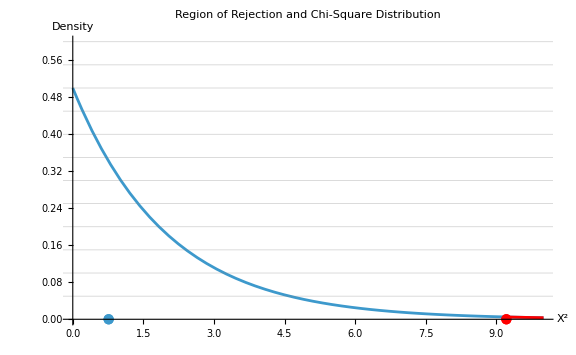

```mathematica
(*Visualzie the regions of rejection, the critical value, and the test statistic*)
Show[Plot[PDF[ChiSquareDistribution[2],x],{x,0,10},PlotRange->{{0,10},{0,.6}},PlotLabel->Style["Region of Rejection and Chi-Square Distribution",16],AxesLabel->{Style["X^2",14],Style["Density",14]},GridLines->{None,Range[.05,.6,.05]},ImageSize->Large],ListPlot[{{.762,0}}],Plot[PDF[ChiSquareDistribution[2],x],{x,9.21,10},PlotRange->{{9.21,10},{0,.6}},Filling->Axis,PlotStyle->Red],ListPlot[{{9.21,0}},PlotStyle->Red]]
```

The test statistic is in the region of rejection and we reject the null hypothesis and support the alternative hypothesis

-value approach

using =1-CHI.DIST(138.8,2,1)

```mathematica
(*Calculate the p-value*)
1-CDF[ChiSquareDistribution[2],138.8]
```

0.

and we reject the null hypothesis and support the alternative hypothesis

The -value is too small to visualize

Step 7

There is enough evidence in the data at the % level of significance to show that the type of intervention and the response are associated

## SIMULATIONS

We can simulate the distributions of the estimated risk difference, relative risk, and the odds ratio

The simulation with data under the null hypothesis has joint probabilities all being

The simulation select  random observations and calculates each measure of association  times

```mathematica
(*Experiment parameters*)
numSimulations=1000;
sampleSize=200;
```

```mathematica
(*Joint probabilities for the contingency table*)
cellProbs={.25,.25,.25,.25}
```

{0.25,0.25,0.25,0.25}

This represents the contingency table (with proportions) below

Two Nominal Variables |  |  | Total
 |  |  | 
 |  |  | 
Total |  |  |

### RISK DIFFERENCE

We simulate  repeated experiments (creating  contingency tables), taking a sample size of  each

```mathematica
(*Simulate 1000 contingency tables of size 200*)
simTables=RandomVariate[MultinomialDistribution[sampleSize,cellProbs],numSimulations];
```

We calculate the estimated risk difference for each of the  contingency tables

```mathematica
(* Calculate Risk Difference: n11/(n11 + n12) - n21/(n21 + n22) *)
riskDifferencesMultinomial=Map[(#[[1]]/(#[[1]]+#[[2]]))-(#[[3]]/(#[[3]]+#[[4]]))&,N[simTables]];
```

A density histogram visualizes the distribution of the 1000 simulated, estimated risk differences

A normal distribution model is added to the visualization

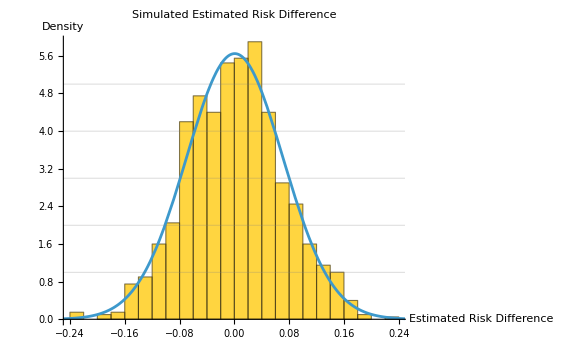

```mathematica
(* Visualize the null distribution *)
Show[Histogram[riskDifferencesMultinomial,Automatic,"PDF",PlotLabel->Style["Simulated Estimated Risk Difference",16],AxesLabel->{Style["Estimated Risk Difference",14],Style["Density",14]},GridLines->{None,Range[1,5,1]},ImageSize->Large],Plot[PDF[NormalDistribution[Mean[riskDifferencesMultinomial],StandardDeviation[riskDifferencesMultinomial]],x],{x,-1/3,1/3}]]
```

### RELATIVE RISK

We simulate  repeated experiments (creating  contingency tables), taking a sample size of  each

```mathematica
(*Simulate 1000 contingency tables of size 200*)
simTables=RandomVariate[MultinomialDistribution[sampleSize,cellProbs],numSimulations];
```

We calculate the estimated relative risk for each of the  contingency tables

```mathematica
(* Calculate relative risk: (n11/(n11 + n12)) / (n21/(n21 + n22))*)
relativeRisksMultinomial=Map[(#[[1]]/(#[[1]]+#[[2]]))/(#[[3]]/(#[[3]]+#[[4]]))&,N[simTables]];
```

A density histogram visualizes the distribution of the 1000 simulated, log-transformed, estimated risk ratios

A normal distribution model is added to the visualization

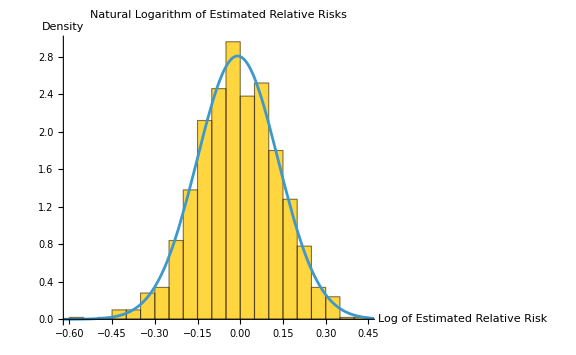

```mathematica
(* Visualize the null distribution *)
Show[Histogram[Log[relativeRisksMultinomial],Automatic,"PDF",PlotLabel->Style["Natural Logarithm of Estimated Relative Risks",16],AxesLabel->{Style["Log of Estimated Relative Risk",14],Style["Density",14]},GridLines->{None,Range[1,3,1/2]},ImageSize->Large],Plot[PDF[NormalDistribution[Mean[Log[relativeRisksMultinomial]],StandardDeviation[Log[relativeRisksMultinomial]]],x],{x,-7/10,7/10}]]
```

### ODDS RATIO

We simulate  repeated experiments (creating  contingency tables), taking a sample size of  each

```mathematica
(*Simulate 1000 contingency tables of size 200*)
simTables=RandomVariate[MultinomialDistribution[sampleSize,cellProbs],numSimulations];
```

We calculate the estimated odds ratio for each of the  contingency tables

```mathematica
(*Calculate odds ratios: (n11 n22) / (n12 n21)*)
oddsRatiosMultinomial=Map[((#[[1]] #[[4]])/(#[[2]] #[[3]]))&,N[simTables]];
```

A density histogram visualizes the distribution of the 1000 simulated, log-transformed, estimated odds ratios

A normal distribution model is added to the visualization

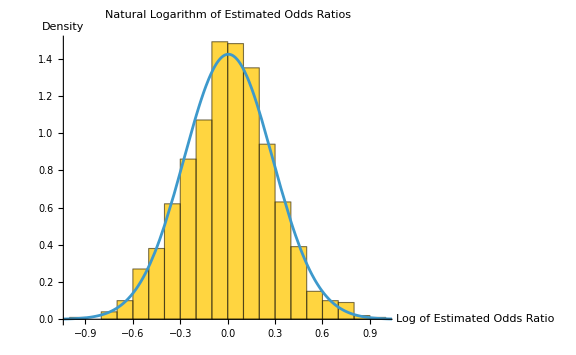

```mathematica
(* Visualize the null distribution *)
Show[Histogram[Log[oddsRatiosMultinomial],Automatic,"PDF",PlotLabel->Style["Natural Logarithm of Estimated Odds Ratios",16],AxesLabel->{Style["Log of Estimated Odds Ratio",14],Style["Density",14]},GridLines->{None,Range[1,7/5,1/5]},ImageSize->Large],Plot[PDF[NormalDistribution[Mean[Log[oddsRatiosMultinomial]],StandardDeviation[Log[oddsRatiosMultinomial]]],x],{x,-3/2,3/2}]]
```